```mathematica
SetDirectory[NotebookDirectory[]];
AppendTo[$Path,NotebookDirectory[]];
Needs["PenroseTilingFunctions`"]
```

```mathematica
darkteal=RGBColor[1/256*{35,55,59}];
alertcolour=RGBColor[1/256*{235,129,27}];
```

```mathematica
checkers=Flatten[Table[Translate[Rectangle[],{i,j}],{i,0,6},{j,0,6}],1];
grid={EdgeForm[{Thin}],FaceForm[Transparent],#}&/@checkers;
blacks=Take[checkers,{1,-1,2}];
whites={White,#}&/@Drop[checkers,{1,-1,2}];
```

```mathematica
Graphics@{darkteal,grid,blacks}
```

-Graphics-

```mathematica
Export["Checkerboard.png",Graphics@{darkteal,grid,blacks},Background->None]
```

Checkerboard.png

```mathematica
Export["tealproto.png",Graphics[{darkteal,Rectangle[]}]]
Export["whiteproto.png",Graphics[{EdgeForm[{darkteal}],FaceForm[None],Rectangle[]}],Background->None]
```

tealproto.png

whiteproto.png

```mathematica
Export["protoset.png",{Graphics[{darkteal,Rectangle[]}],Graphics[{EdgeForm[{darkteal}],FaceForm[None],Rectangle[]}]},Background->None]
```

protoset.png

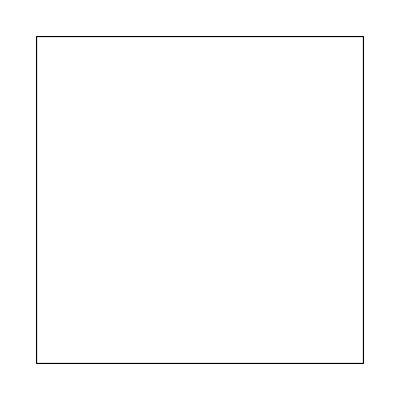
{-Graphics-,-Graphics-}

```mathematica
{Graphics[{darkteal,Rectangle[]}],Graphics[{EdgeForm[{darkteal}],FaceForm[None],Rectangle[]}]}
```

```mathematica
newgrid=Complement[grid,Cases[grid,{EdgeForm[{Thickness[Tiny]}],FaceForm[-Graphics-],Translate[Rectangle[{0,0}],{4,_}]}]];
Translate[#,{0,0.5}]&/@Cases[blacks,Translate[Rectangle[{0,0}],{4,_}]];
Complement[blacks,Cases[blacks,Translate[Rectangle[{0,0}],{4,_}]]];
Graphics[{darkteal,newgrid,%%,%}]
Export["CheckerboardAperiodic.png",%, Background->None]
```

-Graphics-

CheckerboardAperiodic.png

```mathematica
Flatten[Table[Translate[Rectangle[],{i,j}],{i,0,6},{j,0,6}],1];
newblacks=Take[%,{1,-1,3}];
```

```mathematica
Graphics@{darkteal,grid,newblacks}
Export["CheckerboardOther.png",%,Background->None]
```

-Graphics-

CheckerboardOther.png

```mathematica
circles=Flatten[Table[Translate[Disk[],{i,j}],{i,0,7,2},{j,0,7,2}],1];
```

```mathematica
Rotate[Graphics[{FaceForm[darkteal],#}&/@circles],Pi/4];
Graphics[{darkteal,Rotate[circles,Pi/4]}];
Table[Graphics[{darkteal,Translate[Rotate[circles,Pi/4],{0,i*2Sqrt[2]}]}],{i,-2,1}];
Show[{%,%%},PlotRange->{{-2.3,8.3},{-3.75,6.85}}]
Export["CheckerboardCircles.png",%]
```

-Graphics-

CheckerboardCircles.png

```mathematica
Hexagon[x_]:=Line[x+#&/@(Through[{Cos,Sin}[Pi#/3]]&/@Range[0,6])]

HexagonalGrid[x_,y_]:=Module[{i,j},
Table[Hexagon[{3/2i,Sqrt[3]j+Mod[i,2]Sqrt[3]/2}],{i,x},{j,y}]
]
```

```mathematica
Graphics[{darkteal,Thick,#}&/@Flatten[HexagonalGrid[7,7],1],
PlotRange->{{.7,10.2},{.7,10.2}}]
Export["Hexagons.png",%,Background->None]
```

-Graphics-

Hexagons.png

```mathematica
Graphics[{Thick,darkteal,Hexagon[1]}]
Export["HexagonProto.png",%,Background->None]
```

-Graphics-

HexagonProto.png

```mathematica
Present:=Graphics[{Transpose[{((IfFat[#1,darkteal,alertcolour]&)/@#1&)[#1],Polygon/@Coor/@Δ/@#1}]}]&
```

```mathematica
Present@FullInflate[{unitfat},0]
Export["FatProto.png",%,Background->None]
Present@FullInflate[{unitskinny},0]
Export["SkinnyProto.png",%,Background->None]
```

-Graphics-

FatProto.png

-Graphics-

SkinnyProto.png